```mathematica
Ep = 940;
```

```mathematica
measCond = 0.989*^-9;
```

```mathematica
(*measCond = 1.40*^-9; PREVIOUSLY*)
```

```mathematica
preFactor = 2.680594*^-08;
```

```mathematica
qMaxF[Ep_,Tm_]:=1+2(√(Ep/Tm))/Erfc[-√(Ep/Tm)] NIntegrate[Erfc[x],{x,-√(Ep/Tm),∞}]
```

```mathematica
funker[Ep_,Tm_,κ_,Kmeas_]:=Kmeas/preFactor * √Tm *qMaxF[Ep,Tm]*((κ-3/2)^(1/2)Gamma[κ-1/2])/Gamma[κ];
```

```mathematica
kappas={1.52,1.6,1.75,2.0,2.45,4,10,1000};
```

```mathematica
tick = 0.002;
```

```mathematica
styles=Reverse[Flatten@Table[{Directive[Dotted,color,Thickness[tick]],Directive[Dashed,color,Thickness[tick]],Directive[DotDashed,color,Thickness[tick]],Directive[Dotted,color,Thickness[tick]]},{color,{Black,Gray}}]];
```

```mathematica
styles[[8]]=Directive[Black,Thickness[tick]];
```

```mathematica
placeList={Scaled[1.1],Below,Below,Below,Below,Below,Below,Scaled[2]};
```

```mathematica
nDigs={4,3,3,3,3,3,3,3};
```

```mathematica
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,8}];
```

```mathematica
kapStrVals[[5]] = StringForm["κ_t (≃ 2.45)"];
```

```mathematica
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,8}];
```

```mathematica
kappaLabels[[8]]=StringForm[" "];
```

```mathematica
minDens=1.73;
maxDens=2.07;
minT=73.14;
maxT= 153.68;
```

Part::partw: Part 9 of … does not exist.

Part::partw: Part 9 of {κ = 1.52,κ = 1.6,κ = 1.75,κ = 2.,κ = κ_t (≃ 2.45),κ = 4,κ = 10, } does not exist.

Part::partw: Part 9 of {Scaled[1.1],Below,Below,Below,Below,Below,Below,Scaled[2]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

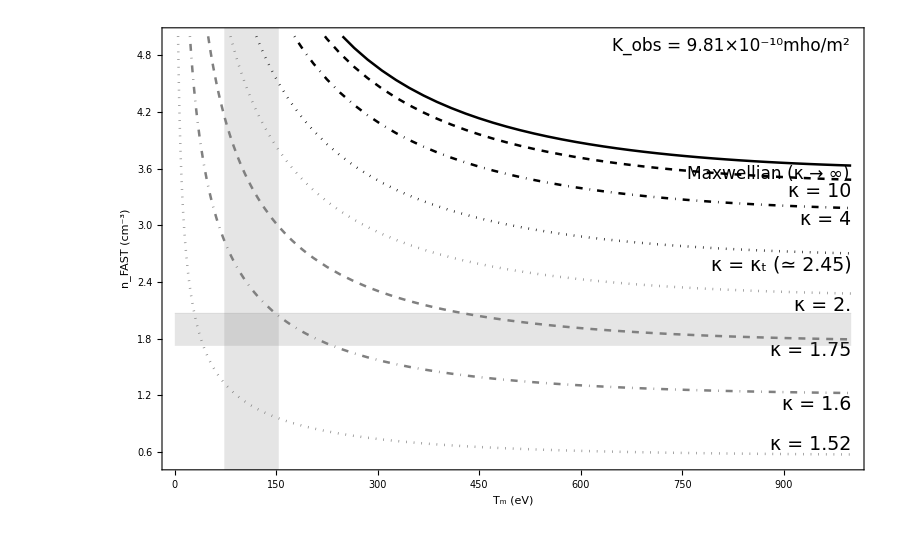

```mathematica
Show[Table[Plot[funker[Ep,Tm,kappas[[k]],measCond],{Tm,1,1000},PlotStyle->styles[[k]],PlotLegends->LineLegend[Automatic],Epilog->{Text[Style["K_obs = 9.81×10^-10mho/m^2",FontSize->17],Scaled[{0.98,0.98}],{1,1}],Text[Style["Maxwellian (κ → ∞)",FontSize->17],Scaled[{0.98,0.69}],{1,1}]},PlotRange->{{1,999},{0.5,5}},PlotRangeClipping->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2,3,4,5,6,7,8,9}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```